```mathematica
{897,6985,{3,{4,5,7,10,9},{5<->9,5<->10},{{4,5,9},{5,9,10},{5,7,10}}}}
```

```mathematica
{32637,279676,{3,{1,7,5,13,12},{7<->12,7<->13},{{1,7,12},{7,12,13},{5,7,13}}}}
```

```mathematica
VertexList[applied]
```

{1,2,3,7,12,9,11,6,8,4,5,10,13,14}

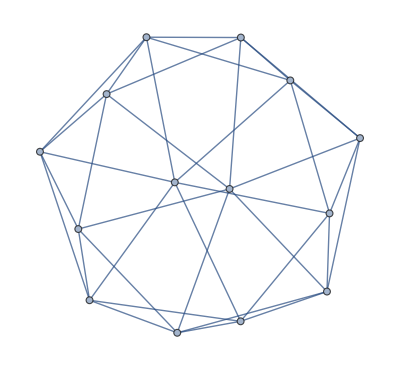

```mathematica
applied=Rule3[ReadGrof[32637],{7<->12,7<->13},{1,7,5,13,12}]
```

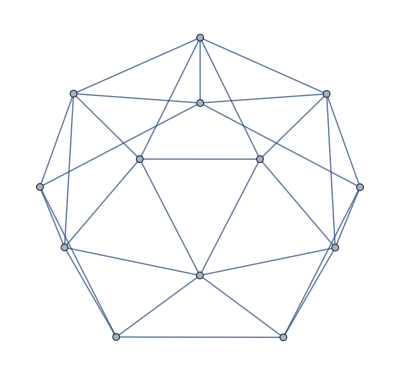

```mathematica
CenterRemoved=VertexDelete[applied,14]
```

```mathematica
MaximalPlanarQ[CenterRemoved]
```

False

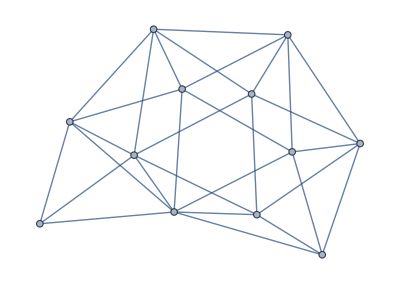

```mathematica
firstContracted=VertexContract[CenterRemoved,{7,12}]
```

```mathematica
MaximalPlanarQ[firstContracted]
```

True

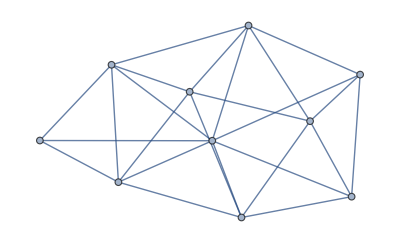

```mathematica
secondContracted=VertexContract[CenterRemoved,{4,7}]
```

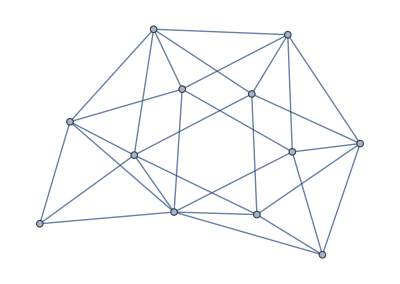

```mathematica
secondContracted2=VertexContract[CenterRemoved,{1,13}]
```

```mathematica
MaximalPlanarQ[secondContracted2]
```

True

```mathematica
IsomorphicGraphQ[secondContracted,secondContracted2]
```

False

```mathematica
MaximalPlanarQ[firstContracted]
```

True

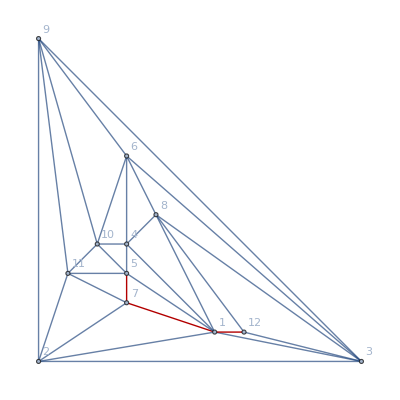

```mathematica
Graph[secondContracted2,GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlight->Rule3Cycle[{1,7,5,13,12}]]
```

```mathematica
EdgeList[%114]
```

{1<->2,1<->3,1<->7,1<->11,2<->3,2<->6,2<->9,3<->6,3<->8,3<->11,5<->7,5<->8,5<->11,6<->8,6<->9,7<->11,8<->11,4<->1,4<->2,4<->5,4<->6,4<->7,4<->8,4<->9}

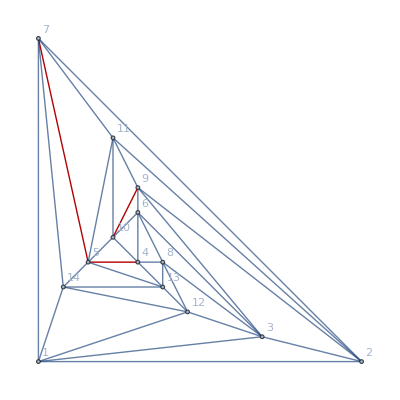

```mathematica
Graph[applied,GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlight->Rule3Cycle[{4,5,7,10,9}]]
```

```mathematica
{32637,279676,{3,{1,7,5,13,12},{7<->12,7<->13},{{1,7,12},{7,12,13},{5,7,13}}}}
```

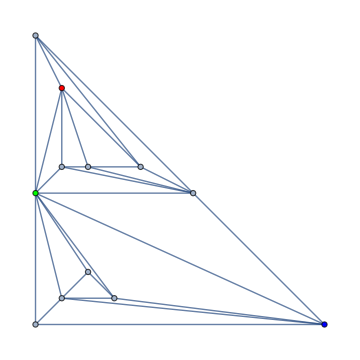
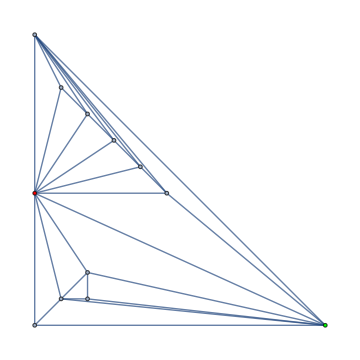
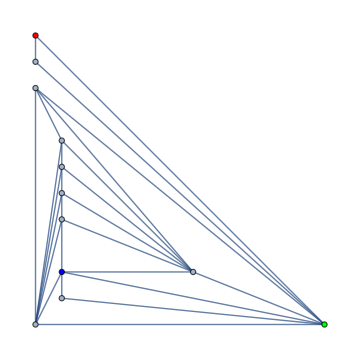
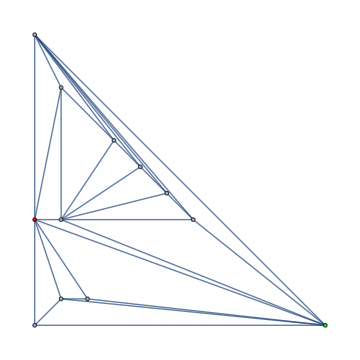
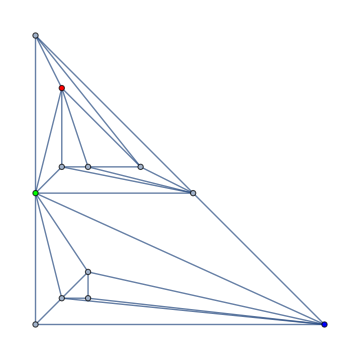
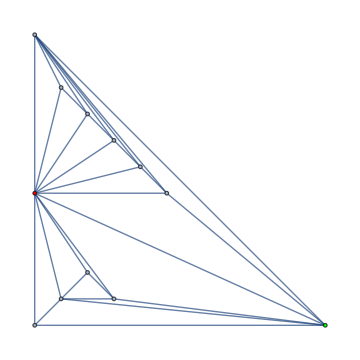
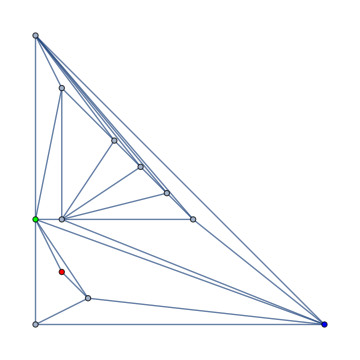
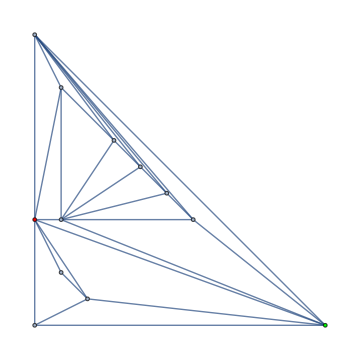
{{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol},{-Graphics-,-Graphics-,pol}}

```mathematica
Monitor[
Table[
With[
{record=deps3[[k]]},
Block[{g,applied, center, first, second, edges=record[[3,3]], cycle=record[[3,2]], max,p1,p2},
g=ReadGrof[record[[1]]];
applied = Rule3[g,edges, cycle];
max=Max[VertexList[applied]];
center = VertexDelete[applied,max];
first=Graph[VertexContract[center,{cycle[[1]],cycle[[3]]}],VertexStyle->{cycle[[2]]->Red,cycle[[1]]->Green, cycle[[4]]->Blue}, VertexSize->Medium];
second=Graph[VertexContract[center,{cycle[[2]],cycle[[4]]}],VertexStyle->{cycle[[2]]->Red,cycle[[1]]->Green}];
p1=PlanarGraphQ[first];
p2=PlanarGraphQ[second];If[!(p1&&p2),Print[record]];
{
Graph[first,GraphLayout->"PlanarEmbedding", ImageSize->Medium],
Graph[second,GraphLayout->"PlanarEmbedding", ImageSize->Medium], "pol"}
]
],
{k,2100000,2100010}
],k]
```

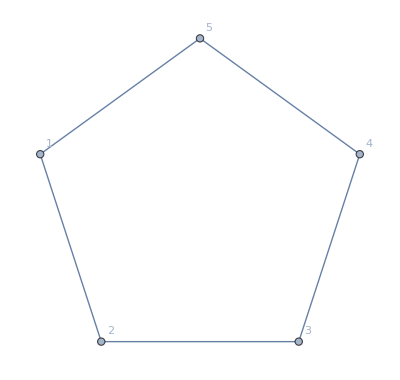

```mathematica
Graph[CycleGraph[5],VertexLabels->"Name"]
```

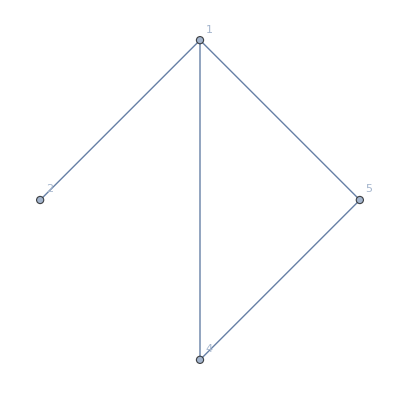

```mathematica
Graph[VertexContract[CycleGraph[5],{1,3}],VertexLabels->"Name"]
```

```mathematica
Monitor[
Table[
With[
{record=deps3[[k]]},
Block[{g,applied, center, first, second, edges=record[[3,3]], cycle=record[[3,2]], max,p1,p2},
g=ReadGrof[record[[1]]];
applied = Rule3[g,edges, cycle];
max=Max[VertexList[applied]];
center = VertexDelete[applied,max];
first=Graph[VertexContract[center,{cycle[[1]],cycle[[3]]}],VertexStyle->{cycle[[2]]->Red,cycle[[4]]->Green,cycle[[5]]->Green}, VertexSize->Medium];
second=Graph[VertexContract[center,{cycle[[2]],cycle[[4]]}],VertexStyle->{cycle[[2]]->Red,cycle[[1]]->Green,cycle[[5]]->Green}];
p1=PlanarGraphQ[first];
p2=PlanarGraphQ[second];If[!(p1&&p2),Print[record]];
1
]
],
{k,1,2436995}
]//Total,k]
```

```mathematica
Length[deps3Bis]
```

3376051

```mathematica
Monitor[
Table[
With[
{record=deps3Bis[[k]]},
Block[{g,applied, center, first, second, edges=record[[3,3]], cycle=record[[3,2]], max,p1,p2},
g=ReadGrof[record[[1]]];
applied = Rule3[g,edges, cycle];
max=Max[VertexList[applied]];
center = VertexDelete[applied,max];
first=Graph[VertexContract[center,{cycle[[1]],cycle[[3]]}],VertexStyle->{cycle[[2]]->Red,cycle[[4]]->Green,cycle[[5]]->Green}, VertexSize->Medium];
second=Graph[VertexContract[center,{cycle[[2]],cycle[[4]]}],VertexStyle->{cycle[[2]]->Red,cycle[[1]]->Green,cycle[[5]]->Green}];
p1=PlanarGraphQ[first];
p2=PlanarGraphQ[second];If[!(p1&&p2),Print[record]];
1
]
],
{k,1,3376051}
]//Total,k]
```

3376051

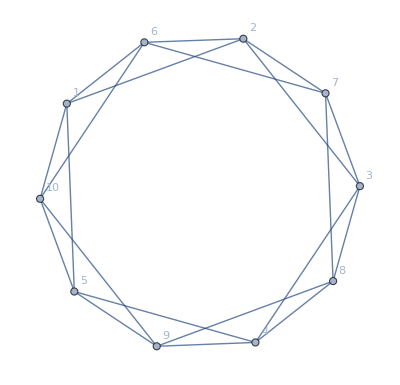

```mathematica
Graph[EdgeAdd[CycleGraph[5],{1<->6,6<->2,2<->7,7<->3,3<->8,8<->4,4<->9,9<->5,5<->10,10<->1,6<->7,7<->8,8<->9,9<->10,10<->6}],VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

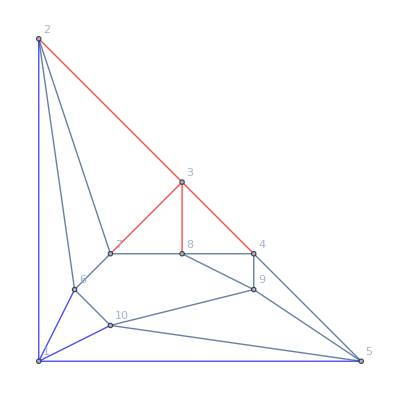

```mathematica
Graph[EdgeAdd[CycleGraph[5],{1<->6,6<->2,2<->7,7<->3,3<->8,8<->4,4<->9,9<->5,5<->10,10<->1,6<->7,7<->8,8<->9,9<->10,10<->6}],VertexLabels->"Name", GraphLayout->"PlanarEmbedding",EdgeStyle->{1<->6->Blue,1<->10->Blue,1<->2->Blue,1<->5->Blue,
3<->7->Red,3<->8->Red,3<->2->Red,3<->4->Red}]
```

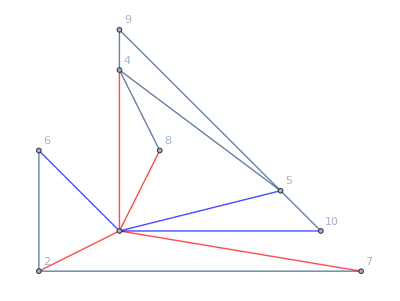

```mathematica
Graph[VertexContract[ Graph[EdgeAdd[CycleGraph[5],{1<->6,6<->2,2<->7,7<->3,3<->8,8<->4,4<->9,9<->5,5<->10,10<->1}],VertexLabels->"Name", GraphLayout->"PlanarEmbedding",EdgeStyle->{1<->6->Blue,1<->10->Blue,1<->2->Blue,1<->5->Blue,
1<->7->Red,1<->8->Red,1<->2->Red,1<->4->Red}],{1,3}],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

```mathematica
VertexContract[Graph[VertexContract[ Graph[EdgeAdd[CycleGraph[5],{1<->6,6<->2,2<->7,7<->3,3<->8,8<->4,4<->9,9<->5,5<->10,10<->1}],VertexLabels->"Name", EdgeStyle->{1<->6->Blue,1<->10->Blue,1<->2->Blue,1<->5->Blue,
1<->7->Red,1<->8->Red,1<->2->Red,1<->4->Red}],{1,3}],VertexLabels->"Name"],{2,4}]//PlanarGraphQ
```

True